# DAKOTA User's Manual Graphics Chapter 2 - Tutorial Created by S.L. Brown, 20 June 2006

## Preliminaries

Set the working directory to the directory that this checked out copy of tutorial-image-generator.nb is in.

```mathematica
SetDirectory[ToFileName[Extract["FileName"/.NotebookInformation[EvaluationNotebook[]],{1},FrontEnd`FileName]]];
```

## Rosenbrock's Function

### Visualization

```mathematica
rosen[x_,y_]:=100 (y-x^2)^2+(1-x)^2
```

```mathematica
rosensurf=Plot3D[rosen[x,y],{x,-2,2},{y,-2,2},
AxesLabel->{Subscript[x, 1],Subscript[x, 2] ,""},
ImageSize->600,
PlotRange->{0,4000},
TextStyle->{FontFamily->"Times",FontSize->24}]
```

-Graphics3D-

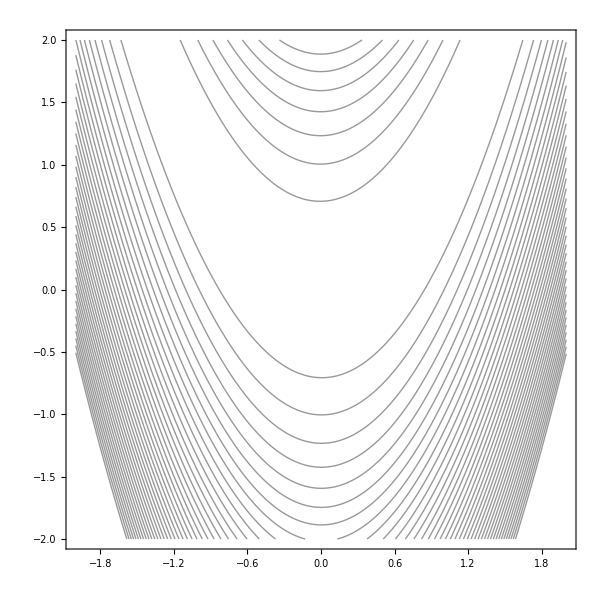

```mathematica
rosencont=ContourPlot[rosen[x,y],{x,-2,2},{y,-2,2},
Contours->40,
ContourShading->False,
ImageSize->600,
PlotPoints->50,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

### Parameter Studies

#### 2-D Parameter Study Data

```mathematica
data2d=Import["../../examples/users/2d.out.sav","Table"];
```

```mathematica
data2dPTS=Transpose[{First/@Select[data2d,MatchQ[#,{_,"x1"}]&],First/@Select[data2d,MatchQ[#,{_,"x2"}]&]}];
```

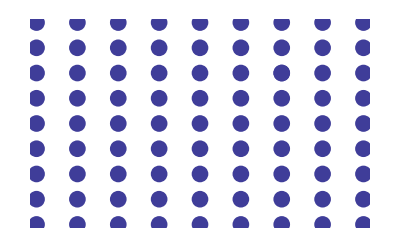

```mathematica
plot2dPTS=ListPlot[data2dPTS,
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

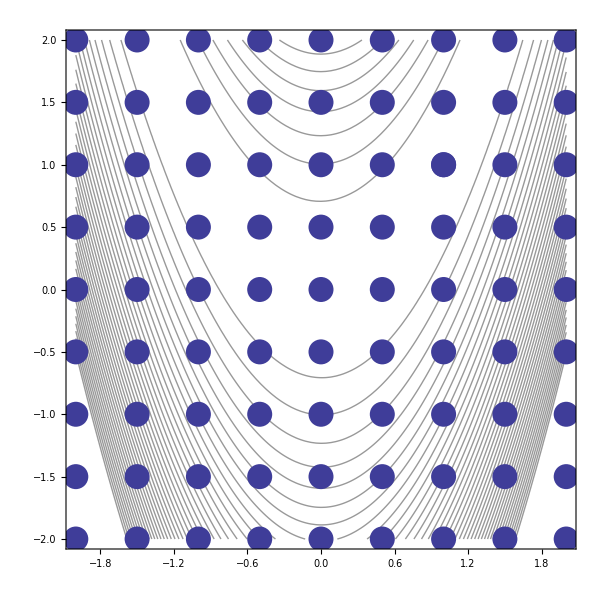

```mathematica
rosen2dpts=Show[rosencont,plot2dPTS,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

#### Vector Parameter Study Data

```mathematica
datavec=Import["../../examples/users/vector.out.sav","Table"];
```

```mathematica
datavecPTS=Transpose[{First/@Select[datavec,MatchQ[#,{_,"x1"}]&],First/@Select[datavec,MatchQ[#,{_,"x2"}]&]}];
```

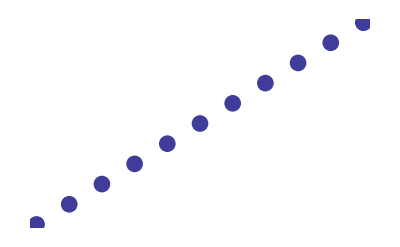

```mathematica
plotvecPTS=ListPlot[datavecPTS,
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

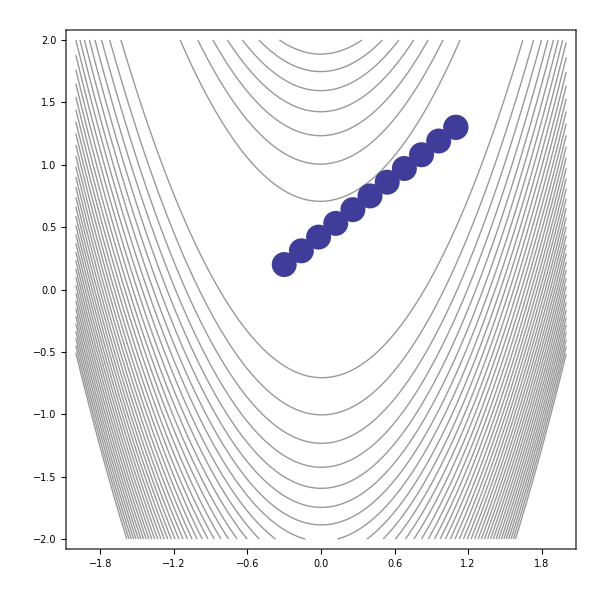

```mathematica
rosenvectpts=Show[rosencont,plotvecPTS,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

### Optimization

#### Gradient-based Unconstrained Optimization

```mathematica
datauncon=Import["../../examples/users/grad_opt.out.sav","Table"];
```

```mathematica
dataunconPTS=Rest/@Select[datauncon,MatchQ[#,{"1)",_,_}]&];
```

We're only taking the data after the first three points (line search).

```mathematica
plotunconPTS=ListPlot[Take[dataunconPTS,-(Length[dataunconPTS]-3)],
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

-Graphics-

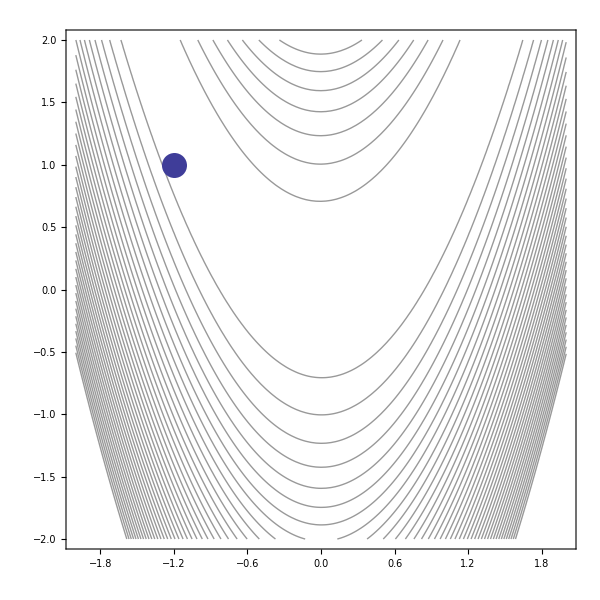

```mathematica
rosenunconpts=Show[rosencont,plotunconPTS,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

#### Nongradient-based Optimization via Pattern Search

```mathematica
dataps=Import["../../examples/users/ps_opt.out.sav","Table"];
```

```mathematica
datapsPTS=Transpose[{First/@Select[dataps,MatchQ[#,{_,"x1"}]&],First/@Select[dataps,MatchQ[#,{_,"x2"}]&]}];
```

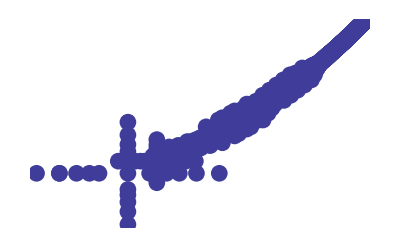

```mathematica
plotpsPTS=ListPlot[datapsPTS,
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

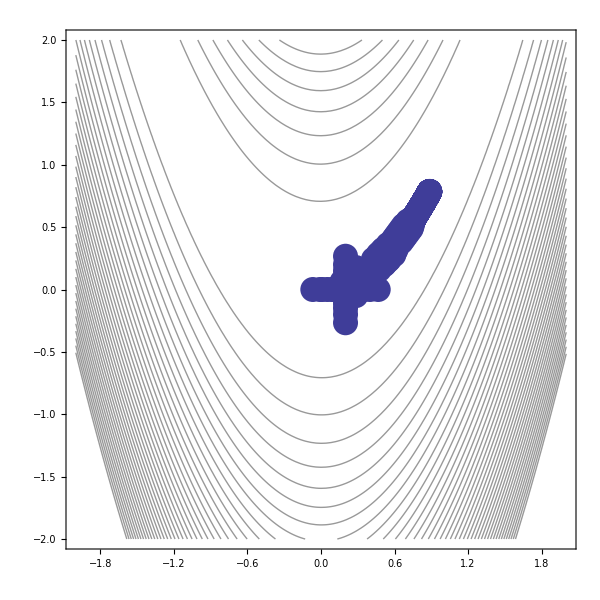

```mathematica
rosenpspts=Show[rosencont,plotpsPTS,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

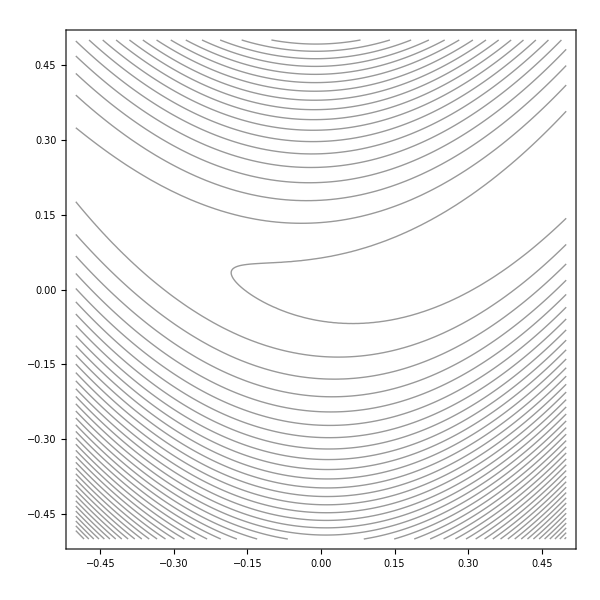

```mathematica
rosencontclose=ContourPlot[rosen[x,y],{x,-0.5,0.5},{y,-0.5,0.5},
AspectRatio->1,
Contours->40,
ContourShading->False,
ImageSize->600,
PlotPoints->50,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

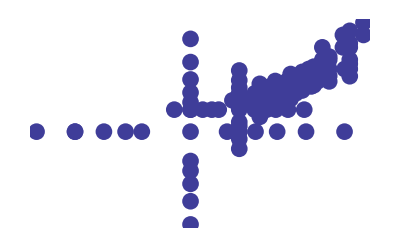

```mathematica
plotpsPTSclose=ListPlot[Select[Select[datapsPTS,First[#]<0.5&],Last[#]<0.5&],
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

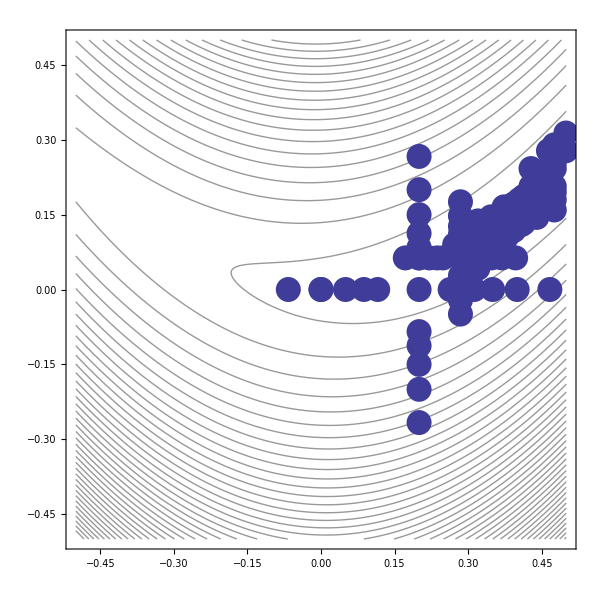

```mathematica
rosenpsptsclose=Show[rosencontclose,plotpsPTSclose,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

#### Nongradient-based Optimization via Evolutionary Algorithm

```mathematica
dataea=Import["../../examples/users/ea_opt.out.sav","Table"];
```

```mathematica
dataeaPTS=Transpose[{First/@Select[dataea,MatchQ[#,{_,"x1"}]&],First/@Select[dataea,MatchQ[#,{_,"x2"}]&]}];
```

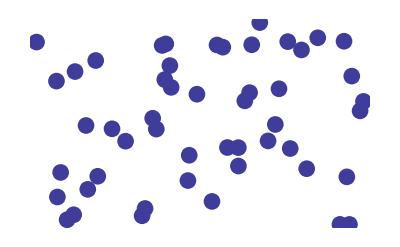

```mathematica
ploteaPTSinit=ListPlot[Take[dataeaPTS,50],
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

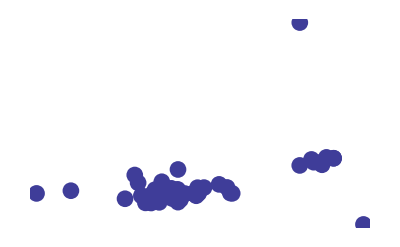

```mathematica
ploteaPTSfinal=ListPlot[Take[dataeaPTS,-50],
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

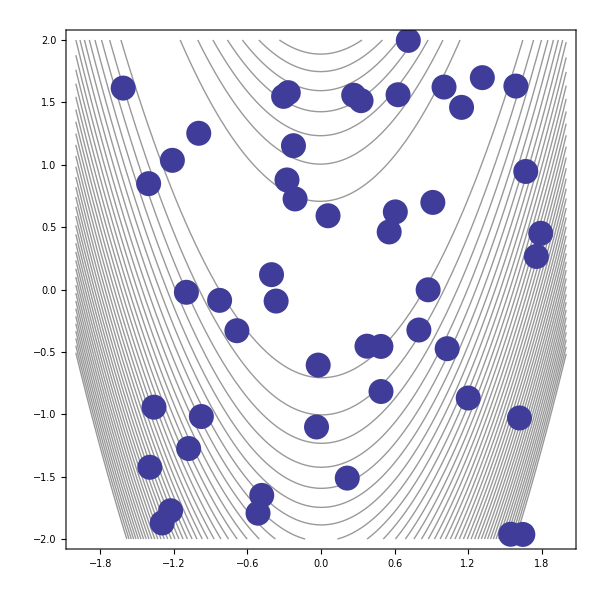

```mathematica
roseneaptsinit=Show[rosencont,ploteaPTSinit,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

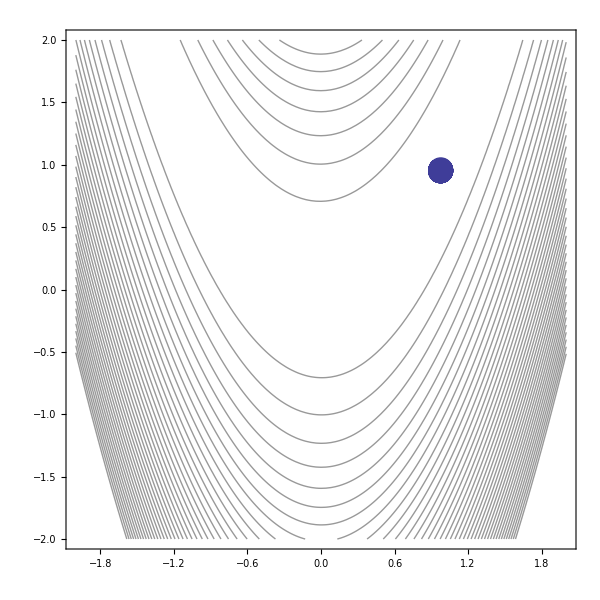

```mathematica
roseneaptsfinal=Show[rosencont,ploteaPTSfinal,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

### Sampling

#### Monte Carlo

```mathematica
datamc=Import["../../examples/users/nond.out.sav","Table"];
```

```mathematica
datamcPTS=Transpose[{First/@Select[datamc,MatchQ[#,{_,"x1"}]&],First/@Select[datamc,MatchQ[#,{_,"x2"}]&]}];
```

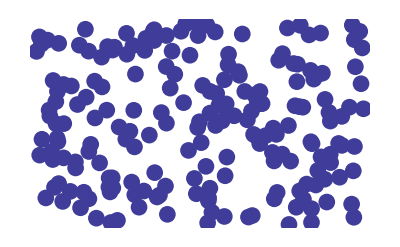

```mathematica
plotmcPTS=ListPlot[datamcPTS,
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

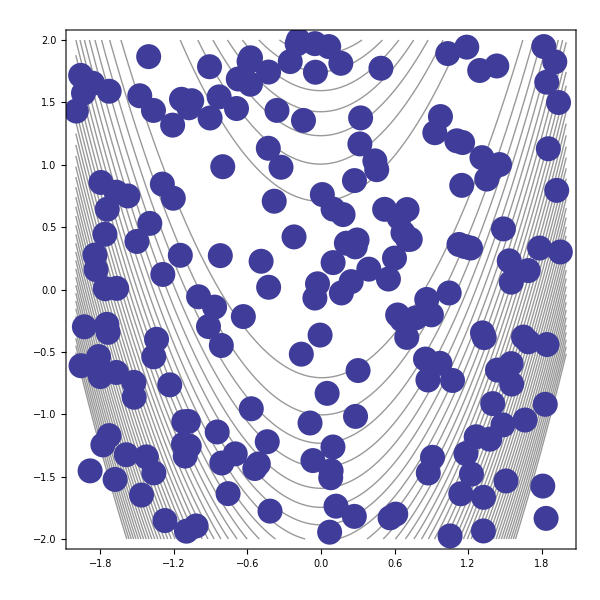

```mathematica
rosencontmcPTS=Show[rosencont,plotmcPTS,
AspectRatio->1,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

## Textbook Function

### Visualization

```mathematica
textbook[x_,y_]:=(x-1)^4+(y-1)^4
```

```mathematica
g1[t_]:={t/4,t^2/8}
```

```mathematica
g2[t_]:={t^2/8,t/4}
```

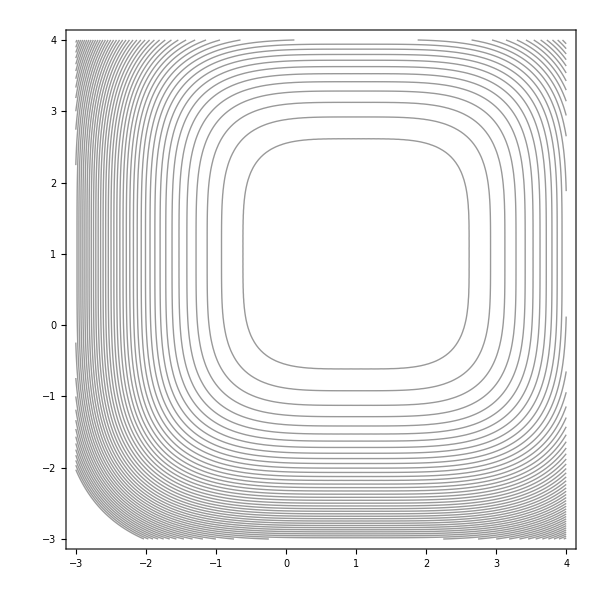

```mathematica
textbookcont=ContourPlot[textbook[x,y],{x,-3,4},{y,-3,4},
Contours->50,
ContourShading->False,
ImageSize->600,
PlotPoints->50,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

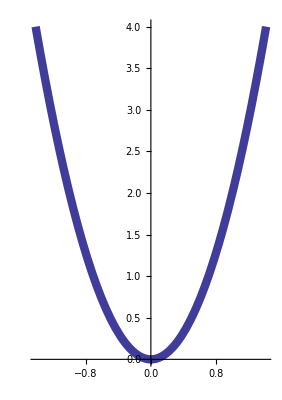

```mathematica
g1param=ParametricPlot[g1[t],{t,-Sqrt[32],Sqrt[32]},
PlotStyle->{{Thickness[0.015]}}]
```

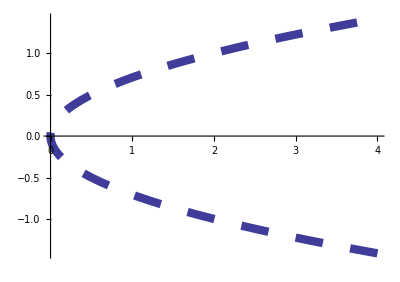

```mathematica
g2param=ParametricPlot[g2[t],{t,-Sqrt[32],Sqrt[32]},
PlotStyle->{{Thickness[0.015],Dashing[{0.05,0.05}]}}]
```

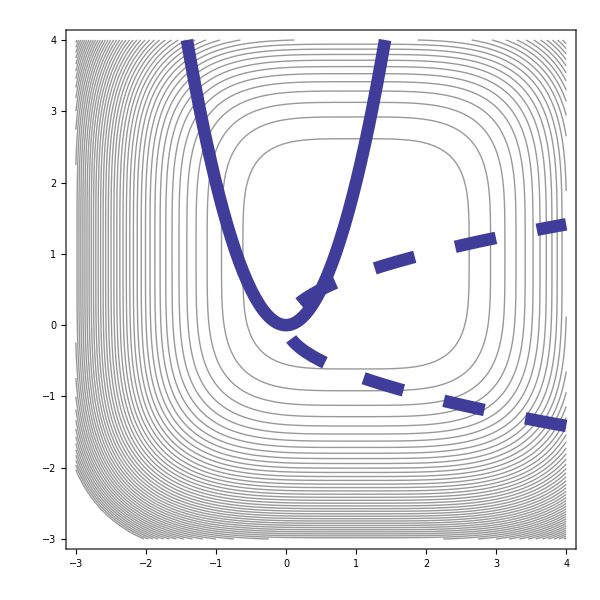

```mathematica
tbconscont=Show[textbookcont,g1param,g2param,
Axes->False,
AspectRatio->1,
Frame->True,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

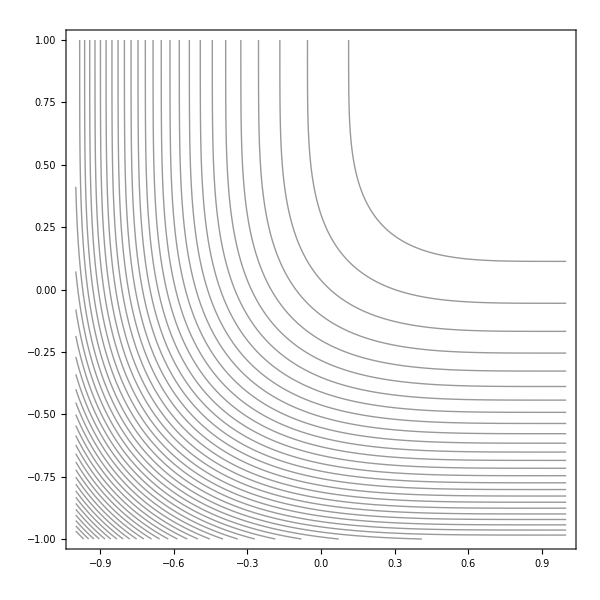

```mathematica
textbookconscontclose=ContourPlot[textbook[x,y],{x,-1,1},{y,-1,1},
Contours->50,
ContourShading->False,
ImageSize->600,
PlotPoints->50,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

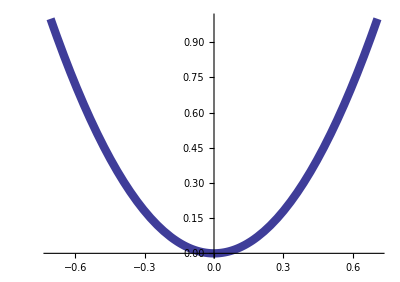

```mathematica
g1paramclose=ParametricPlot[g1[t],{t,-Sqrt[8],Sqrt[8]},
PlotStyle->{{Thickness[0.015]}}]
```

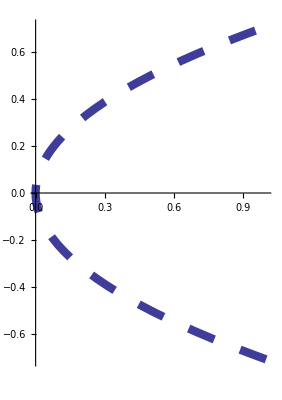

```mathematica
g2paramclose=ParametricPlot[g2[t],{t,-Sqrt[8],Sqrt[8]},
PlotStyle->{{Thickness[0.015],Dashing[{0.05,0.05}]}}]
```

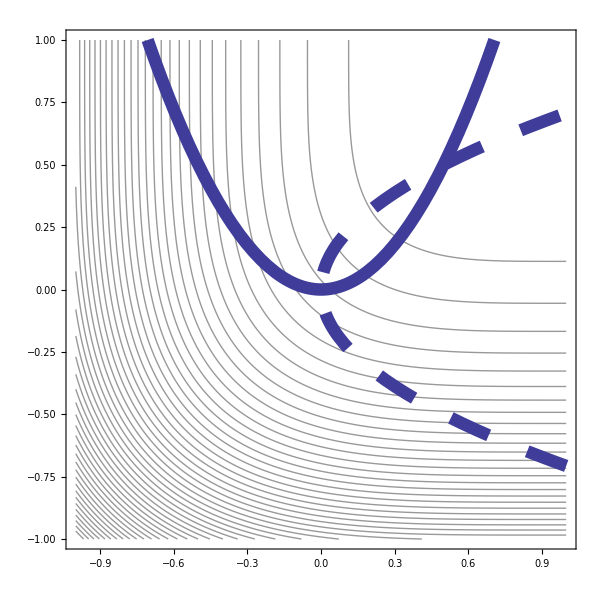

```mathematica
tbconscontclose=Show[textbookconscontclose,g1paramclose,g2paramclose,
Axes->False,
AspectRatio->1,
Frame->True,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

### Optimization

#### Gradient-based Constrained Optimization

```mathematica
datatbcon=Import["../../examples/users/textbook.out.sav","Table"];
```

```mathematica
datatbconPTS=Transpose[{First/@Select[datatbcon,MatchQ[#,{_,"x1"}]&],First/@Select[datatbcon,MatchQ[#,{_,"x2"}]&]}];
```

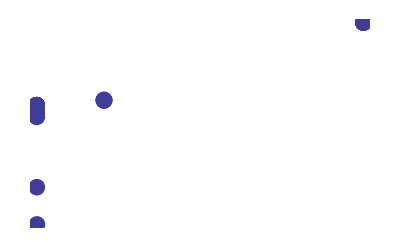

```mathematica
plottbconPTS=ListPlot[datatbconPTS,
Axes->False,
PlotStyle->{PointSize[0.03]}]
```

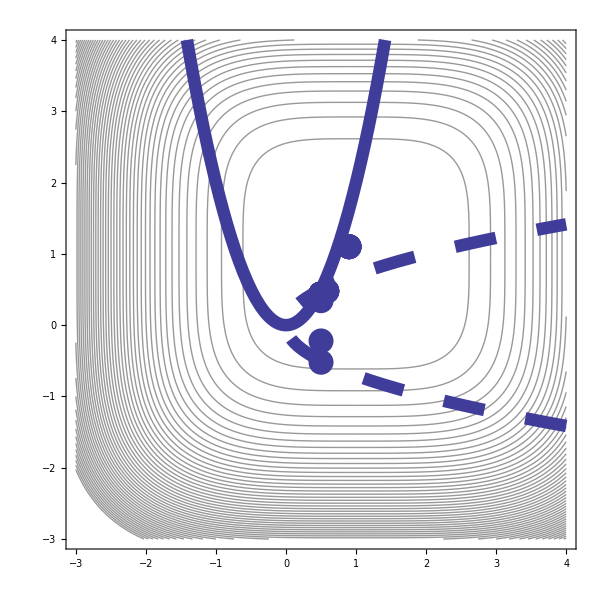

```mathematica
tbconsoptcont=Show[textbookcont,g1param,g2param,plottbconPTS,
Axes->False,
AspectRatio->1,
Frame->True,
ImageSize->600,
TextStyle->{FontFamily->"Times",FontSize->24}]
```

## Uncertainty Quantification

```mathematica
<<Graphics`MultipleListPlot`
```

General::obspkg: Graphics`MultipleListPlot` is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

### Sampling

```mathematica
lhsgraphicdata=data={{0.2,0.2},{0.7,0.3},{0.8,0.7},{0.3,0.9}};
```

```mathematica
data10lhssamples=Import["../../examples/users/uq_users_0.out.sav","Table"];
```

```mathematica
data5lhssamples=Import["../../examples/users/uq_users_1.out.sav","Table"];
```

```mathematica
data10randomsamples=Import["../../examples/users/uq_users_2.out.sav","Table"];
```

```mathematica
data5randomsamples=Import["../../examples/users/uq_users_3.out.sav","Table"];
```

```mathematica
lhsgraphicPTS = ListPlot[data,
AspectRatio->1,
Axes->False,
AxesOrigin->{0,0},
Frame->True,
GridLines->{Table[0.25 i,{i,0,4}],Table[0.25 i,{i,0,4}]},
FrameLabel->{Subscript[x, 1],Subscript[x, 2]},
FrameTicks->{{0,1},{0,1},None,None},
ImageSize->600,
PlotRange->{{0,1},{0,1}},
PlotStyle->{PointSize[0.03]},
RotateLabel->False,
TextStyle->{FontFamily->"Times",FontSize->24}];
```

```mathematica
data10lhsPTS=Transpose[{First/@Select[data10lhssamples,MatchQ[#,{_,"x1"}]&],First/@Select[data10lhssamples,MatchQ[#,{_,"x2"}]&]}];
```

```mathematica
data5lhsPTS=Transpose[{First/@Select[data5lhssamples,MatchQ[#,{_,"x1"}]&],First/@Select[data5lhssamples,MatchQ[#,{_,"x2"}]&]}];
```

```mathematica
data10randomPTS=Transpose[{First/@Select[data10randomsamples,MatchQ[#,{_,"x1"}]&],First/@Select[data10randomsamples,MatchQ[#,{_,"x2"}]&]}];
```

```mathematica
data5randomPTS=Transpose[{First/@Select[data5randomsamples,MatchQ[#,{_,"x1"}]&],First/@Select[data5randomsamples,MatchQ[#,{_,"x2"}]&]}];
```

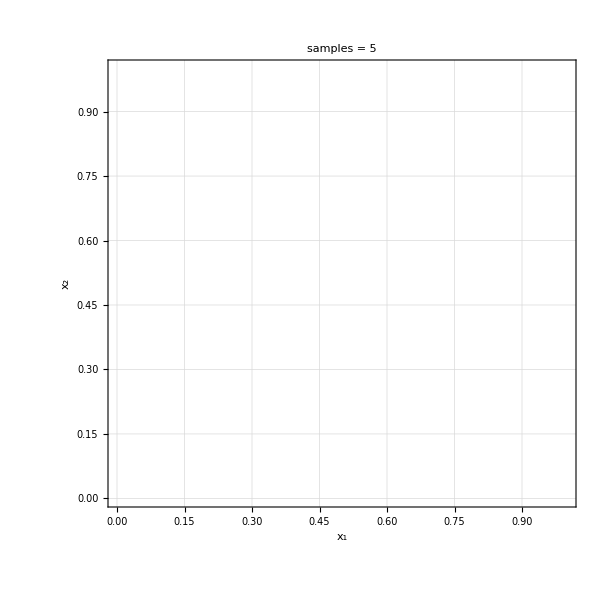

```mathematica
plot5uqPTS=MultipleListPlot[data5lhsPTS,data5randomPTS,
AspectRatio->1,
Axes->False,
Frame->True,
FrameLabel->{Subscript[x, 1],Subscript[x, 2] },
GridLines->Automatic,
ImageSize->600,
PlotLabel->"samples = 5",
PlotRange->{{0,1},{0,1}},
RotateLabel->False,
TextStyle->{FontFamily->"Times",FontSize->24},
SymbolShape->{MakeSymbol[{Line[{{5,0},{-5,0}}],Line[{{0,5},{0,-5}}]}],PlotSymbol[Triangle,8,Filled->False]}]
```

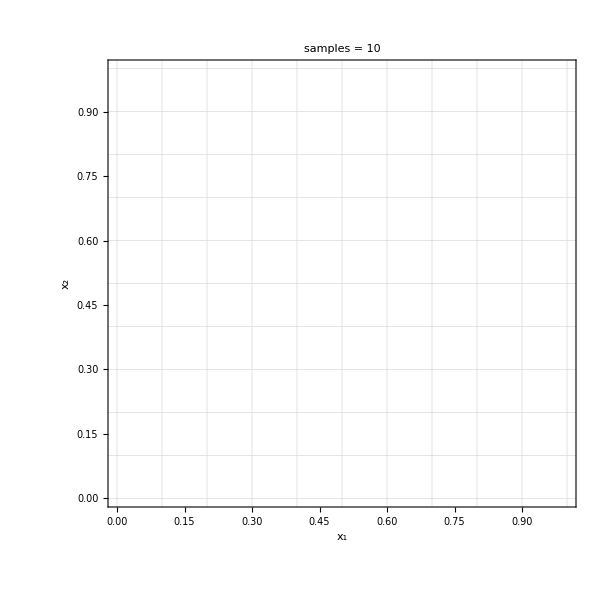

```mathematica
plot10uqPTS=MultipleListPlot[data10lhsPTS,data10randomPTS,
AspectRatio->1,
Axes->False,
Frame->True,
FrameLabel->{Subscript[x, 1],Subscript[x, 2] },
FrameTicks->Automatic,
GridLines->{Table[0.1 i,{i,0,10}],Table[0.1 i,{i,0,10}]},
ImageSize->600,
PlotLabel->"samples = 10",
PlotRange->{{0,1},{0,1}},
RotateLabel->False,
TextStyle->{FontFamily->"Times",FontSize->24},
SymbolShape->{MakeSymbol[{Line[{{5,0},{-5,0}}],Line[{{0,5},{0,-5}}]}],PlotSymbol[Triangle,8,Filled->False]}]
```

## Image Output

```mathematica
Export["images/rosen_3d_surf."<>#,rosensurf]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_2d_surf."<>#,rosencont]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_2d_pts."<>#,rosen2dpts]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_vect_pts."<>#,rosenvectpts]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_grad_opt_pts."<>#,rosenunconpts]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_ps_opt_pts."<>#,rosenpspts]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_ps_opt_pts2."<>#,rosenpsptsclose]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_ea_init."<>#,roseneaptsinit]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_ea_final."<>#,roseneaptsfinal]&/@{"eps","png"};
```

```mathematica
Export["images/rosen_nond_pts."<>#,rosencontmcPTS]&/@{"eps","png"};
```

```mathematica
Export["images/textbook_contours."<>#,tbconscont]&/@{"eps","png"};
```

```mathematica
Export["images/textbook_closeup."<>#,tbconscontclose]&/@{"eps","png"};
```

```mathematica
Export["images/textbook_history."<>#,tbconsoptcont]&/@{"eps","png"};
```

```mathematica
Export["images/lhs_graphic."<>#,lhsgraphicPTS]&/@{"eps","png"};
```

```mathematica
Export["images/input_samples5."<>#,plot5uqPTS]&/@{"eps","png"};
```

```mathematica
Export["images/input_samples10."<>#,plot10uqPTS]&/@{"eps","png"};
```